Created by Alison Ord 10 June 2014 for Hobbs and Ord (2015) Structural Geology: The Mechanics of Deforming Rocks

starting with Chapter_3_Kinematics_14 and also 17.nb

1. the deformation - displacement in Lagrangian space

```mathematica
t=1;
```

```mathematica
datapts3=Graphics[Line[Table[{t x+(1/Sqrt[3])  y,y/t},{y,10},{x,10}]],Axes->True, PlotRange->{{6,66},{0,3}},AxesOrigin->{6,0},Ticks->{Automatic,{0,1,2,3}}];
```

```mathematica
datapts4=Graphics[Line[Table[{t x+(1/Sqrt[3])  y,y/t},{x,10},{y,10}]],Axes->True, PlotRange->{{6,66},{0,3}},AxesOrigin->{6,0},Ticks->{Automatic,{0,1,2,3}}];
```

```mathematica
Show[datapts3,datapts4,ImageSize->Large]
```

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{-x*((1-t)/t)+(t*y/Sqrt[3]),-y*(t-1)},imagescale},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->Red,ColorFunction->"BeachColors",LightingAngle->0,LineIntegralConvolutionScale->10]
```

-Graphics-

2. the deformation - velocity in Lagrangian space

```mathematica
t=1;
```

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{x/t^2+y/Sqrt[3],-y},imagescale},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->Red,ColorFunction->"BeachColors",LightingAngle->0,LineIntegralConvolutionScale->10]
```

-Graphics-

Construct a matrix l which is the velocity gradient in spatial coordinates.

```mathematica
l=SparseArray[{{1,1},{1,2},{2,1},{2,2}}->{1/ttt^2,1/Sqrt[3],0,-1}]
```

SparseArray[<3>,{2,2}]

```mathematica
MatrixForm[l]
```

(1/ttt^2 | 1/(√3)
0 | -1)

```mathematica
Eigenvalues[l]
```

{1/ttt^2,-1}

```mathematica
Eigenvectors[l]
```

{{1,0},{-ttt^2/(√3 (1+ttt^2)),1}}

```mathematica
ttt=6;
```

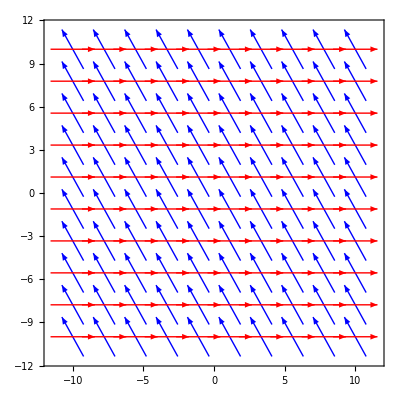

```mathematica
VectorPlot[{{-ttt^2/(√3 (1+ttt^2)),1},{1,0}},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->{Blue,Red}]
```

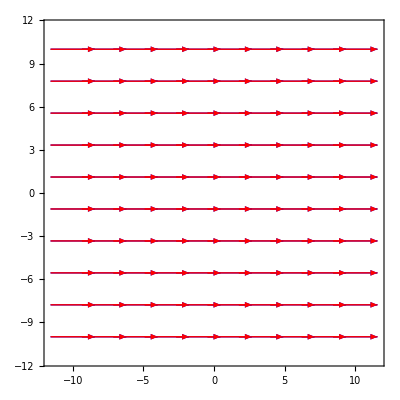

```mathematica
VectorPlot[{{1,0},{1,0}},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->{Blue,Red}]
```

```mathematica
lmf=Normal[l]
```

{{1/ttt,-1/(√3)},{0,-1/ttt}}

Calculate the Transpose of the matrix l

```mathematica
ltranspose=Transpose[l]
```

SparseArray[<3>,{2,2}]

```mathematica
ltransposemf=Normal[ltranspose]
```

{{1/ttt,0},{-1/(√3),-1/ttt}}

```mathematica
d=lmf/2+ltransposemf/2
```

{{1/ttt,-1/(2 √3)},{-1/(2 √3),-1/ttt}}

```mathematica
Eigenvalues[d]
```

{-(√(12+ttt^2))/(2 √3 ttt),(√(12+ttt^2))/(2 √3 ttt)}

```mathematica
Eigenvectors[d]
```

{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},{-(6+√3 √(12+ttt^2))/(√3 ttt),1}}

```mathematica
ttt=1;
```

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},imagescale},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->Red,ColorFunction->"BeachColors",LightingAngle->0,LineIntegralConvolutionScale->10]
```

-Graphics-

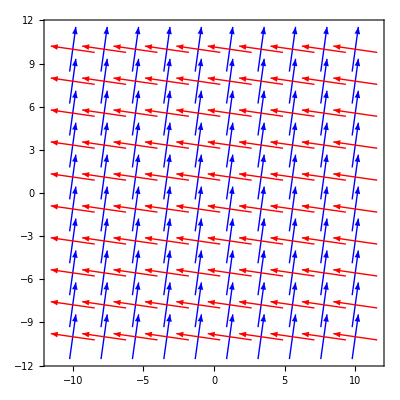

```mathematica
VectorPlot[{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},{-(6+√3 √(12+ttt^2))/(√3 ttt),1}},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->{Blue,Red}]
```

```mathematica
ttt=3;
```

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},imagescale},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->Red,ColorFunction->"BeachColors",LightingAngle->0,LineIntegralConvolutionScale->10]
```

-Graphics-

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{-(6+√3 √(12+ttt^2))/(√3 ttt),1},imagescale},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->Red,ColorFunction->"BeachColors",LightingAngle->0,LineIntegralConvolutionScale->10]
```

-Graphics-

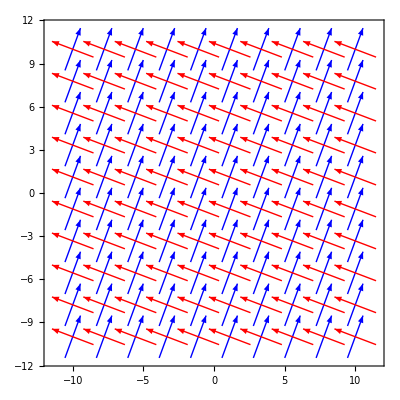

```mathematica
VectorPlot[{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},{-(6+√3 √(12+ttt^2))/(√3 ttt),1}},{x,-10,10},{y,-10,10},VectorPoints->10,VectorStyle->{Blue,Red}]
```

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{(-6+√3 √(12+ttt^2))/(√3 ttt),1},imagescale},{x,-1,1},{y,-1,1},StreamPoints->Fine,StreamScale->Large,StreamStyle->Yellow,ColorFunction->GrayLevel,LightingAngle->0,LineIntegralConvolutionScale->3]
```

-Graphics-

```mathematica
imagescale={Automatic,500,128};
LineIntegralConvolutionPlot[{{-(6+√3 √(12+ttt^2))/(√3 ttt),1},imagescale},{x,-1,1},{y,-1,1},StreamPoints->Fine,StreamScale->Large,StreamStyle->Yellow,ColorFunction->GrayLevel,LightingAngle->0,LineIntegralConvolutionScale->3]
```

-Graphics-